```mathematica
(*Rectangular Waveguide Modes*)
```

```mathematica
SetDirectory["C:\\Users\\Alex Brinson\\Documents\\Ph106c\\Animations\\RectangularWaveguideModes"] ;
```

```mathematica
tmRect[a_,b_,m_,n_,x_,y_]:=Sin[(m π x)/a] Sin[(n π y)/b]
teRect[a_,b_,m_,n_,x_,y_]:=Cos[(m π x)/a] Cos[(n π y)/b]
ωcRect[m_,n_,ϵ_,μ_,a_,b_]:=1/(√(ϵ μ))π √((m/a)^2+ (n/b)^2);  (*cutoff frequency*)
kRect[m_,n_,ω_,ϵ_,μ_,a_,b_]:=ω*√(ϵ μ)*√(1-(ωcRect[m,n,ϵ,μ,a,b]/ω)^2);
ePerpTMRect[m_,n_,x_,y_,ω_,a_,b_,ϵ_,μ_]:=((*I*) kRect[m,n,ω,ϵ,μ,a,b])/(π^2((m/a)^2+ (n/b)^2)) Grad[tmRect[a,b,m,n,x,y],{x,y}]
ePerpTMRect3D[m_,n_,x_,y_,ω_,a_,b_,ϵ_,μ_]:=(I kRect[m,n,ω,ϵ,μ,a,b])/(π^2((m/a)^2+ (n/b)^2))*Append[ Grad[tmRect[a,b,m,n,x,y],{x,y}],0];
hPerpTMRect[m_,n_,x_,y_,ω_,a_,b_,ϵ_,μ_]:=(1(*I*) ω ϵ)/(π^2((m/a)^2+ (n/b)^2))  Cross[{0,0,1}, Append[Grad[tmRect[a,b,m,n,x,y],{x,y}],0]][[1;;2]]
hPerpTMRect3D[m_,n_,x_,y_,ω_,a_,b_,ϵ_,μ_]:=(I ω ϵ)/(π^2((m/a)^2+ (n/b)^2))Cross[{0,0,1}, Append[Grad[tmRect[a,b,m,n,x,y],{x,y}],0]]
eTotTMRect[m_,n_,x_,y_,ω_,a_,b_,ϵ_,μ_]:=ePerpTMRect3D[m,n,x,y,ω,a,b,ϵ,μ]+{0,0,tmRect[a,b,m,n,x,y]}
eTotTMPropRect[m_,n_,x_,y_,ω_,a_,b_,ϵ_,μ_,z_,t_]:=ePerpTMRect3D[m,n,x,y,ω,a,b,ϵ,μ]*(I Sin[kRect[m,n,ω,ϵ,μ,a,b]z-ω t])+{0,0,tmRect[a,b,m,n,x,y]}*Cos[kRect[m,n,ω,ϵ,μ,a,b]z-ω t]
ePerpTERect[m_,n_,x_,y_,ω_,a_,b_,ϵ_,μ_]:=(-1 (*I*) ω μ)/(π^2((m/a)^2+ (n/b)^2)) Cross[{0,0,1}, Append[Grad[teRect[a,b,m,n,x,y],{x,y}],0]][[1;;2]];
ePerpTERect3D[m_,n_,x_,y_,ω_,a_,b_,ϵ_,μ_]:=(-I ω μ)/(π^2((m/a)^2+ (n/b)^2)) Cross[{0,0,1}, Append[Grad[teRect[a,b,m,n,x,y],{x,y}],0]]
hPerpTERect[m_,n_,x_,y_,ω_,a_,b_,ϵ_,μ_]:=((*I*) kRect[m,n,ω,ϵ,μ,a,b])/(π^2((m/a)^2+ (n/b)^2))Grad[teRect[a,b,m,n,x,y],{x,y}];
hPerpTERect3D[m_,n_,x_,y_,ω_,a_,b_,ϵ_,μ_]:=(I kRect[m,n,ω,ϵ,μ,a,b])/(π^2((m/a)^2+ (n/b)^2))*Append[ Grad[teRect[a,b,m,n,x,y],{x,y}],0];
hTotTERect[m_,n_,x_,y_,ω_,a_,b_,ϵ_,μ_]:=hPerpTERect3D[m,n,x,y,ω,a,b,ϵ,μ]+{0,0,teRect[a,b,m,n,x,y]}
hTotTEPropRect[m_,n_,x_,y_,ω_,a_,b_,ϵ_,μ_,z_,t_]:=hPerpTERect3D[m,n,x,y,ω,a,b,ϵ,μ]*(I Sin[kRect[m,n,ω,ϵ,μ,a,b]z-ω t])+{0,0,teRect[a,b,m,n,x,y]}*Cos[kRect[m,n,ω,ϵ,μ,a,b]z-ω t]
(* aPlot and bPlot are the plot settings used for the waveguide's length (x-tent) and width (y), respectively *)
aPlot=2;bPlot=1;
```

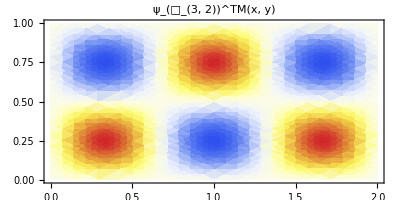

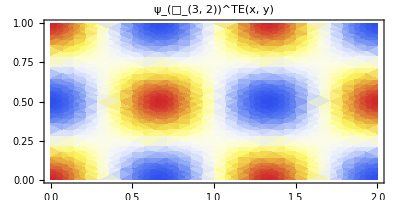

```mathematica
DensityPlot[tmRect[aPlot,bPlot,3,2,x,y],{x,0,aPlot},{y,0,bPlot},AspectRatio->bPlot/aPlot,ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotLabel->"ψ_(□_(3, 2))^TM(x, y)"]
DensityPlot[teRect[aPlot,bPlot,3,2,x,y],{x,0,aPlot},{y,0,bPlot},AspectRatio->bPlot/aPlot,ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotLabel->"ψ_(□_(3, 2))^TE(x, y)"]
```

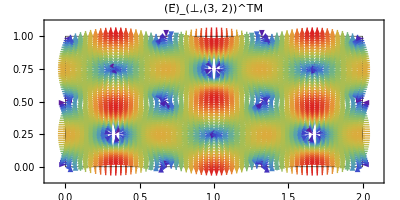
{0.850767,-Graphics-}

```mathematica
AbsoluteTiming[Show[VectorPlot[ePerpTMRect[3,2,ξ,ψ,10,aPlot,bPlot,1,1]/.{ξ->x,ψ->y},{x,0,aPlot},{y,0,bPlot},PlotRange->{{-.1,aPlot+.1},{-.1,bPlot+.1}},VectorPoints->{60,60},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.015],VectorScale->.06,PlotLabel->"(E⃗)_(⊥,(3, 2))^TM",AspectRatio->bPlot/aPlot],Graphics[{Thickness[.001],Line[{{0,0},{aPlot,0},{aPlot,bPlot},{0,bPlot},{0,0}}]}]]]
```

```mathematica
AbsoluteTiming[Show[VectorPlot[Evaluate[ePerpTMRect[3,2,x,y,10,aPlot,bPlot,1,1]],{x,0,aPlot},{y,0,bPlot},PlotRange->{{-.1,aPlot+.1},{-.1,bPlot+.1}},VectorPoints->{60,60},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.015],VectorScale->.06,PlotLabel->"(E⃗)_(⊥,(3, 2))^TM",AspectRatio->bPlot/aPlot],Graphics[{Thickness[.001],Line[{{0,0},{aPlot,0},{aPlot,bPlot},{0,bPlot},{0,0}}]}]]] (*Today I learned how to use Evaluate[] *)
```

{0.0520676,-Graphics-}

```mathematica
f32TM=Function[{x,y},Evaluate[ePerpTMRect[3,2,x,y,10,aPlot,bPlot,1,1]]] (*This is just so my plot commands won't be so hard to read*)
(*plotOps ={ PlotRange->{{-.1,aPlot+.1},{-.1,bPlot+.1}},VectorPoints->{60,60},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.015],VectorScale->.06,AspectRatio->bPlot/aPlot}*)
```

Function[{x,y},{(12 √(1-π^2/16) Cos[(3 π x)/2] Sin[2 π y])/(5 π),(16 √(1-π^2/16) Cos[2 π y] Sin[(3 π x)/2])/(5 π)}]

```mathematica
AbsoluteTiming[Show[VectorPlot[f32TM[x,y],{x,0,aPlot},{y,0,bPlot},PlotRange->{{-.1,aPlot+.1},{-.1,bPlot+.1}},VectorPoints->{60,60},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.015],VectorScale->.06,PlotLabel->"(E⃗)_(⊥,(3, 2))^TM",AspectRatio->bPlot/aPlot],Graphics[{Thickness[.001],Line[{{0,0},{aPlot,0},{aPlot,bPlot},{0,bPlot},{0,0}}]}]]]
```

{0.0541806,-Graphics-}

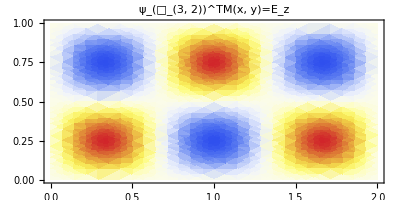

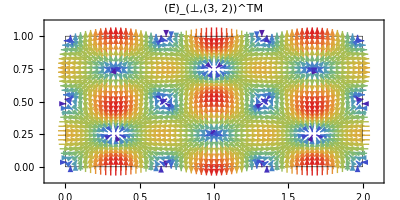

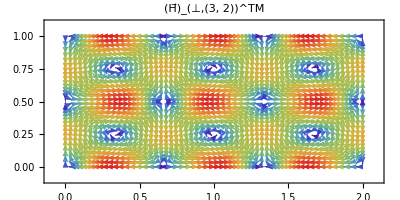

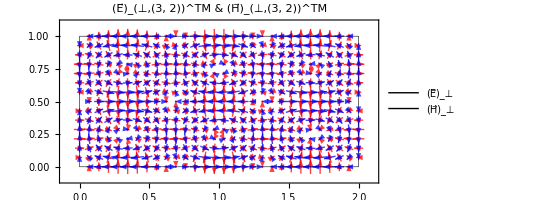

```mathematica
(*Transverse Magnetic Plots*)
DensityPlot[tmRect[aPlot,bPlot,3,2,x,y],{x,0,aPlot},{y,0,bPlot},AspectRatio->bPlot/aPlot,ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotLabel->"ψ_(□_(3, 2))^TM(x, y)=E_z"]

Show[VectorPlot[Evaluate[ePerpTMRect[3,2,x,y,10,aPlot,bPlot,1,1]],{x,0,aPlot},{y,0,bPlot},PlotRange->{{-.1,aPlot+.1},{-.1,bPlot+.1}},VectorPoints->{60,30},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.015],VectorScale->.06,AspectRatio->bPlot/aPlot,PlotLabel->"(E⃗)_(⊥,(3, 2))^TM"],
Graphics[{Thickness[.001],Line[{{0,0},{aPlot,0},{aPlot,bPlot},{0,bPlot},{0,0}}]}]]

Show[VectorPlot[Evaluate[hPerpTMRect[3,2,x,y,10,aPlot,bPlot,1,1]],{x,0,aPlot},{y,0,bPlot},PlotRange->{{-.1,aPlot+.1},{-.1,bPlot+.1}},VectorPoints->{60,30},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.015],VectorScale->.06,AspectRatio->bPlot/aPlot,PlotLabel->"(H⃗)_(⊥,(3, 2))^TM"],Graphics[{Thickness[.001],Line[{{0,0},{aPlot,0},{aPlot,bPlot},{0,bPlot},{0,0}}]}]]

ePerpPlotTM=VectorPlot[Evaluate[ePerpTMRect[3,2,x,y,10,aPlot,bPlot,1,1]],{x,0,aPlot},{y,0,bPlot},PlotRange->{{-.1,aPlot+.1},{-.1,bPlot+.1}},VectorPoints->{30,15},VectorStyle->{Red,Arrowheads[0.015],Opacity[0.75]},VectorScale->.05,PlotLegends->{"(E⃗)_⊥",Red}];
bPerpPlotTM=VectorPlot[Evaluate[hPerpTMRect[3,2,x,y,10,aPlot,bPlot,1,1]],{x,0,aPlot},{y,0,bPlot},PlotRange->{{-.1,aPlot+.1},{-.1,bPlot+.1}},VectorPoints->{30,15},VectorStyle->{Blue,Arrowheads[0.015],Opacity[0.75]},VectorScale->.05,PlotLegends->{"(H⃗)_⊥",Blue}];
Show[ePerpPlotTM,bPerpPlotTM,Graphics[{Thickness[.001],Line[{{0,0},{aPlot,0},{aPlot,bPlot},{0,bPlot},{0,0}}]}],AspectRatio->bPlot/aPlot,PlotLabel->"(E⃗)_(⊥,(3, 2))^TM & (H⃗)_(⊥,(3, 2))^TM"]
```

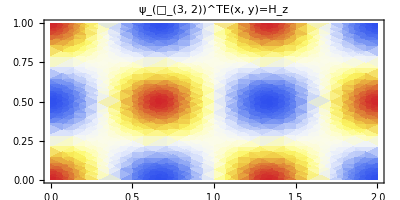

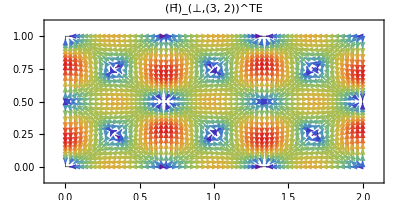

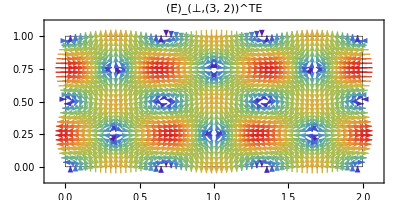

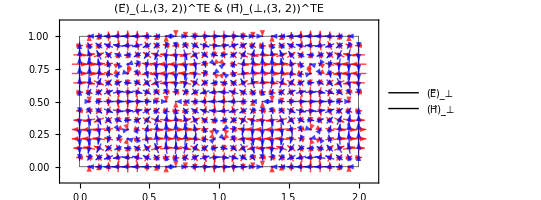

```mathematica
(*Transverse Electric Plots*)
DensityPlot[teRect[aPlot,bPlot,3,2,x,y],{x,0,aPlot},{y,0,bPlot},AspectRatio->bPlot/aPlot,ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotLabel->"ψ_(□_(3, 2))^TE(x, y)=H_z"]

Show[VectorPlot[Evaluate[hPerpTERect[3,2,x,y,10,aPlot,bPlot,1,1]],{x,0,aPlot},{y,0,bPlot},PlotRange->{{-.1,aPlot+.1},{-.1,bPlot+.1}},VectorPoints->{60,30},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.015],VectorScale->.06,AspectRatio->bPlot/aPlot,PlotLabel->"(H⃗)_(⊥,(3, 2))^TE"],
Graphics[{Thickness[.001],Line[{{0,0},{aPlot,0},{aPlot,bPlot},{0,bPlot},{0,0}}]}]]

Show[VectorPlot[Evaluate[ePerpTERect[3,2,x,y,10,aPlot,bPlot,1,1]],{x,0,aPlot},{y,0,bPlot},PlotRange->{{-.1,aPlot+.1},{-.1,bPlot+.1}},VectorPoints->{60,30},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.015],VectorScale->.06,PlotLabel->"(E⃗)_(⊥,(3, 2))^TE",AspectRatio->bPlot/aPlot],Graphics[{Thickness[.001],Line[{{0,0},{aPlot,0},{aPlot,bPlot},{0,bPlot},{0,0}}]}]]

ePerpPlotTE=VectorPlot[Evaluate[ePerpTERect[3,2,x,y,10,aPlot,bPlot,1,1]],{x,0,aPlot},{y,0,bPlot},PlotRange->{{-.1,aPlot+.1},{-.1,bPlot+.1}},VectorPoints->{30,15},VectorStyle->{Red,Arrowheads[0.015],Opacity[0.75]},VectorScale->.05,PlotLegends->{"(E⃗)_⊥",Red}];
bPerpPlotTE=VectorPlot[Evaluate[hPerpTERect[3,2,x,y,10,aPlot,bPlot,1,1]],{x,0,aPlot},{y,0,bPlot},PlotRange->{{-.1,aPlot+.1},{-.1,bPlot+.1}},VectorPoints->{30,15},VectorStyle->{Blue,Arrowheads[0.015],Opacity[0.75]},VectorScale->.05,PlotLegends->{"(H⃗)_⊥",Blue}];
Show[ePerpPlotTE,bPerpPlotTE,Graphics[{Thickness[.001],Line[{{0,0},{aPlot,0},{aPlot,bPlot},{0,bPlot},{0,0}}]}],AspectRatio->bPlot/aPlot,PlotLabel->"(E⃗)_(⊥,(3, 2))^TE & (H⃗)_(⊥,(3, 2))^TE"]
```

```mathematica
Evaluate[eTotTMPropRect[m,n,x,y,p ωcRect[m,n,ϵ,μ,a,b],a,b,ϵ,μ,z,t]]
```

{-(m √(1-1/p^2) p Cos[(m π x)/a] Sin[(n π y)/b] Sin[√(m^2/a^2+n^2/b^2) √(1-1/p^2) p π z-(√(m^2/a^2+n^2/b^2) p π t)/(√(ϵ μ))])/(a √(m^2/a^2+n^2/b^2)),-(n √(1-1/p^2) p Cos[(n π y)/b] Sin[(m π x)/a] Sin[√(m^2/a^2+n^2/b^2) √(1-1/p^2) p π z-(√(m^2/a^2+n^2/b^2) p π t)/(√(ϵ μ))])/(b √(m^2/a^2+n^2/b^2)),Cos[√(m^2/a^2+n^2/b^2) √(1-1/p^2) p π z-(√(m^2/a^2+n^2/b^2) p π t)/(√(ϵ μ))] Sin[(m π x)/a] Sin[(n π y)/b]}

```mathematica
2  ωcRect[3,2,ϵ,μ,aPlot,bPlot] (* I'm setting ω st the period is a rational number, allowing my gifs to loop seamlessly.*)
```

(5 π)/(√(ϵ μ))

```mathematica
eFieldTM32=Function[{x,y,z,t},Evaluate[eTotTMPropRect[3,2,x,y,2 ωcRect[3,2,ϵ,μ,aPlot,bPlot],aPlot,bPlot,ϵ,μ,z,t]/.{ϵ->1,μ-> 1}]]
```

Function[{x,y,z,t},{3/5 √3 Cos[(3 π x)/2] Sin[2 π y] Sin[5 π t-5/2 √3 π z],4/5 √3 Cos[2 π y] Sin[(3 π x)/2] Sin[5 π t-5/2 √3 π z],Cos[5 π t-5/2 √3 π z] Sin[(3 π x)/2] Sin[2 π y]}]

```mathematica
(*I used Manipulate[] to figure out good plot settings, and then Table[] to generate frames and export them to gif. Just remove the semicolon if you'd like to play around with it yourself.*)
(*P.S. I'm sure this isn't the most efficient way to generate gifs, and occasionally Mathematica will actually crash while compiling the frames. I was considering using something like ImageMagick, but I decided to spend my time elsewhere.*)
Manipulate[Image[Show[SliceVectorPlot3D[eFieldTM32[x,y,z,t],{z==0},{x,0,aPlot},{y,0,bPlot},{z,-.1,.1},VectorPoints->{50,25,1},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.0035],VectorScale->.05,BoxRatios->{aPlot, bPlot, .2},Axes->False,Boxed->False,PlotStyle->Opacity[0.15],ViewPoint->{-.5, -2.4,1.25},PlotLabel->"(E⃗)_(□ 3, 2)^TM, Cross-Section Of Waveguide Interior",BaseStyle->{FontWeight->Bold, FontSize->24}],Graphics3D[{Thickness[.001],Line[{{0,0,0},{aPlot,0,0},{aPlot,bPlot,0},{0,bPlot,0},{0,0,0}}]}],AspectRatio->bPlot/aPlot],ImageSize->{1600,800},ImageResolution->200],{t,0,2/5.,2/5.*1/(10.*5)}];
```

```mathematica
crossSecRecTM32Frames=Table[Image[Show[SliceVectorPlot3D[eFieldTM32[x,y,z,t],{z==0},{x,0,aPlot},{y,0,bPlot},{z,-.1,.1},VectorPoints->{50,25,1},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.0035],VectorScale->.05,BoxRatios->{aPlot, bPlot, .2},Axes->False,Boxed->False,PlotStyle->Opacity[0.15],ViewPoint->{-.5, -2.4,1.25},PlotLabel->"(E⃗)_(□ 3, 2)^TM, Cross-Section Of Waveguide Interior",BaseStyle->{FontWeight->Bold, FontSize->24}],Graphics3D[{Thickness[.001],Line[{{0,0,0},{aPlot,0,0},{aPlot,bPlot,0},{0,bPlot,0},{0,0,0}}]}],AspectRatio->bPlot/aPlot],ImageSize->{1600,800},ImageResolution->200],{t,0,2/5.,2/5.*1/(10.*5)}];
```

```mathematica
Export["RectangularCrossSection_E_TM_3_2.gif",crossSecRecTM32Frames[[1;;Length[crossSecRecTM32Frames]-1]],"AnimationRepetitions"->∞,"DisplayDurations"->6/(Length[crossSecRecTM32Frames]-1)]
```

RectangularCrossSection_E_TM_3_2.gif

```mathematica
(*You can repeat the gif making procedure for different modes, if you'd like. *)
```

```mathematica
eFieldTM41=Function[{x,y,z,t},Evaluate[eTotTMPropRect[4,1,x,y,√5  ωcRect[4,1,ϵ,μ,aPlot,bPlot],aPlot,bPlot,ϵ,μ,z,t]/.{ϵ->1,μ-> 1}]]
```

Function[{x,y,z,t},{(4 Cos[2 π x] Sin[π y] Sin[5 π t-2 √5 π z])/(√5),(2 Cos[π y] Sin[2 π x] Sin[5 π t-2 √5 π z])/(√5),Cos[5 π t-2 √5 π z] Sin[2 π x] Sin[π y]}]

```mathematica
Manipulate[Image[Show[SliceVectorPlot3D[eFieldTM41[x,y,z,t],{z==0},{x,0,aPlot},{y,0,bPlot},{z,-.1,.1},VectorPoints->{48,24,1},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.0035],VectorScale->.05,BoxRatios->{aPlot, bPlot, .2},Axes->False,Boxed->False,PlotStyle->Opacity[0.15],ViewPoint->{-.5, -2.4,1.25},PlotLabel->"(E⃗)_(□ 4,1)^TM, Cross-Section Of Waveguide Interior",BaseStyle->{FontWeight->Bold, FontSize->24}],Graphics3D[{Thickness[.001],Line[{{0,0,0},{aPlot,0,0},{aPlot,bPlot,0},{0,bPlot,0},{0,0,0}}]}],AspectRatio->bPlot/aPlot],ImageSize->{1600,800},ImageResolution->200],{t,0,2/5.,2/5.*1/(10.*5)}];
```

```mathematica
crossSecRecTM41Frames=Table[Image[Show[SliceVectorPlot3D[eFieldTM41[x,y,z,t],{z==0},{x,0,aPlot},{y,0,bPlot},{z,-.1,.1},VectorPoints->{48,24,1},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.0035],VectorScale->.05,BoxRatios->{aPlot, bPlot, .2},Axes->False,Boxed->False,PlotStyle->Opacity[0.15],ViewPoint->{-.5, -2.4,1.25},PlotLabel->"(E⃗)_(□ 4,1)^TM, Cross-Section Of Waveguide Interior",BaseStyle->{FontWeight->Bold, FontSize->24}],Graphics3D[{Thickness[.001],Line[{{0,0,0},{aPlot,0,0},{aPlot,bPlot,0},{0,bPlot,0},{0,0,0}}]}],AspectRatio->bPlot/aPlot],ImageSize->{1600,800},ImageResolution->200],{t,0,2/5.,2/5.*1/(10.*5)}];
```

```mathematica
Export["RectangularCrossSectionTM_4_1.gif",crossSecRecTM41Frames[[1;;Length[crossSecRecTM41Frames]-1]],"AnimationRepetitions"->∞,"DisplayDurations"->8/(Length[crossSecRecTM41Frames]-1)]
```

RectangularCrossSectionTM_4_1.gif

```mathematica
(*same deal, but for transverse electric modes*)
```

```mathematica
hFieldTE32=Function[{x,y,z,t},Evaluate[hTotTEPropRect[3,2,x,y,2  ωcRect[3,2,ϵ,μ,aPlot,bPlot],aPlot,bPlot,ϵ,μ,z,t]/.{ϵ->1,μ-> 1}]]
```

Function[{x,y,z,t},{-3/5 √3 Cos[2 π y] Sin[(3 π x)/2] Sin[5 π t-5/2 √3 π z],-4/5 √3 Cos[(3 π x)/2] Sin[2 π y] Sin[5 π t-5/2 √3 π z],Cos[(3 π x)/2] Cos[2 π y] Cos[5 π t-5/2 √3 π z]}]

```mathematica
Manipulate[Image[Show[SliceVectorPlot3D[hFieldTE32[x,y,z,t],{z==0},{x,0,aPlot},{y,0,bPlot},{z,-.1,.1},VectorPoints->{50,25,1},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.0035],VectorScale->.05,BoxRatios->{aPlot, bPlot, .2},Axes->False,Boxed->False,PlotStyle->Opacity[0.15],ViewPoint->{-.5, -2.4,1.25},PlotLabel->"(H⃗)_(□ 3, 2)^TE , Cross-Section Of Waveguide Interior",BaseStyle->{FontWeight->Bold, FontSize->24}],Graphics3D[{Thickness[.001],Line[{{0,0,0},{aPlot,0,0},{aPlot,bPlot,0},{0,bPlot,0},{0,0,0}}]}],AspectRatio->bPlot/aPlot],ImageSize->{1600,800},ImageResolution->200],{t,0,2/5.,2/5.*1/(10.*5)}];
```

```mathematica
crossSecRecTE32Frames=Table[Image[Show[SliceVectorPlot3D[hFieldTE32[x,y,z,t],{z==0},{x,0,aPlot},{y,0,bPlot},{z,-.1,.1},VectorPoints->{50,25,1},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.0035],VectorScale->.05,BoxRatios->{aPlot, bPlot, .2},Axes->False,Boxed->False,PlotStyle->Opacity[0.15],ViewPoint->{-.5, -2.4,1.25},PlotLabel->"(H⃗)_(□ 3, 2)^TE , Cross-Section Of Waveguide Interior",BaseStyle->{FontWeight->Bold, FontSize->24}],Graphics3D[{Thickness[.001],Line[{{0,0,0},{aPlot,0,0},{aPlot,bPlot,0},{0,bPlot,0},{0,0,0}}]}],AspectRatio->bPlot/aPlot],ImageSize->{1600,800},ImageResolution->200],{t,0,2/5.,2/5.*1/(10.*5)}];
```

```mathematica
Export["RectangularCrossSectionTE_3_2.gif",crossSecRecTE32Frames[[1;;Length[crossSecRecTE32Frames]-1]],"AnimationRepetitions"->∞,"DisplayDurations"->6/(Length[crossSecRecTE32Frames]-1)]
```

RectangularCrossSectionTE_3_2.gif

```mathematica
(*One more for good measure...*)
```

```mathematica
Manipulate[Image[Show[SliceVectorPlot3D[hFieldTE32[x,y,z,t],{z==0},{x,0,aPlot},{y,0,bPlot},{z,-.1,.1},VectorPoints->{50,25,1},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.0035],VectorScale->.05,BoxRatios->{aPlot, bPlot, .2},Axes->False,Boxed->False,PlotStyle->Opacity[0.15],ViewPoint->{0, 0,1.5},PlotLabel->"(H⃗)_(□ 3, 2)^TE , Cross-Section Of Waveguide Interior",BaseStyle->{FontWeight->Bold, FontSize->24}],Graphics3D[{Thickness[.001],Line[{{0,0,0},{aPlot,0,0},{aPlot,bPlot,0},{0,bPlot,0},{0,0,0}}]}],AspectRatio->bPlot/aPlot],ImageSize->{1600,800},ImageResolution->200],{t,0,2/5.,2/5.*1/(10.*5)}];
```

```mathematica
crossSecRecTE32FramesTop=Table[Image[Show[SliceVectorPlot3D[hFieldTE32[x,y,z,t],{z==0},{x,0,aPlot},{y,0,bPlot},{z,-.1,.1},VectorPoints->{50,25,1},VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[0.0035],VectorScale->.05,BoxRatios->{aPlot, bPlot, .2},Axes->False,Boxed->False,PlotStyle->Opacity[0.15],ViewPoint->{0, 0,1.5},PlotLabel->"(H⃗)_(□ 3, 2)^TE , Cross-Section Of Waveguide Interior",BaseStyle->{FontWeight->Bold, FontSize->24}],Graphics3D[{Thickness[.001],Line[{{0,0,0},{aPlot,0,0},{aPlot,bPlot,0},{0,bPlot,0},{0,0,0}}]}],AspectRatio->bPlot/aPlot],ImageSize->{1600,800},ImageResolution->200],{t,0,2/5.,2/5.*1/(10.*5)}];
```

```mathematica
Export["RectangularCrossSectionTE_3_2_TopView.gif",crossSecRecTE32FramesTop[[1;;Length[crossSecRecTE32FramesTop]-1]],"AnimationRepetitions"->∞,"DisplayDurations"->6/(Length[crossSecRecTE32FramesTop]-1)]
```

RectangularCrossSectionTE_3_2_TopView.gif

```mathematica
(*And now let's try showing a full chunk of waveguide, instead of just a cross-section*)
(*guideReg=Triangle[{{0,0},{1,0},{1,1}}]; (*Defines the cavity region for our right-triangular hollow waveguide.*)*)
```

```mathematica
Manipulate[Image[VectorPlot3D[hFieldTE32[x,y,z,t],{x,0,aPlot},{y,0,bPlot},{z,0,8/(5 √3)},VectorColorFunction->"Rainbow",VectorStyle->{Arrowheads[0.006],OpacityFunction->Norm},VectorScale->.06,VectorPoints->{30,15,8},BoxRatios->{aPlot,bPlot,8/(5 √3)},Axes->False,ViewPoint->{-1.5,-5,.5},PlotLabel->"(H⃗)_(3, 2)^TE Propagating Through Rectangular Waveguide",BaseStyle->{FontWeight->Bold, FontSize->24}],ImageSize->{1600,800},ImageResolution->200],{t,0,2/5.,2/5.*1/(10.*5)}];
```

```mathematica
waveguideTE32Frames = Table[Image[VectorPlot3D[hFieldTE32[x,y,z,t],{x,0,aPlot},{y,0,bPlot},{z,0,8/(5 √3)},VectorColorFunction->"Rainbow",VectorStyle->{Arrowheads[0.006],OpacityFunction->Norm},VectorScale->.06,VectorPoints->{30,15,8},BoxRatios->{aPlot,bPlot,8/(5 √3)},Axes->False,ViewPoint->{-1.5,-5,.5},PlotLabel->"(H⃗)_(3, 2)^TE Propagating Through Rectangular Waveguide",BaseStyle->{FontWeight->Bold, FontSize->24}],ImageSize->{1600,800},ImageResolution->200],{t,0,2/5.,2/5.*1/(10.*5)}];
```

```mathematica
Export["RectangularWaveguideTE_3_2_IsometricView2.gif",waveguideTE32Frames[[1;;Length[waveguideTE32Frames]-1]],"AnimationRepetitions"->∞,"DisplayDurations"->6/(Length[waveguideTE32Frames]-1)]
```

RectangularWaveguideTE_3_2_IsometricView2.gif

```mathematica
(*That last one is really cluttered, so let's restrict ourselves to just the surface*)
```

```mathematica
Manipulate[Image[Show[SliceVectorPlot3D[hFieldTE32[x,y,z,t],{y==0},{x,0,aPlot},{y,0,bPlot},{z,0,8/(5 √3)},VectorPoints->{50,1,20},VectorColorFunction->"Rainbow",VectorStyle->{Arrowheads[0.008],OpacityFunction->Norm},VectorScale->.05,BoxRatios->{aPlot, bPlot, 8/(5 √3)},Axes->False,Boxed->False,PlotStyle->{Opacity[0.15],White},ViewPoint->{-3, -5,1},PlotLabel->"(H⃗)_(□ 3, 2)^TE On Waveguide Surface",BaseStyle->{FontWeight->Bold, FontSize->24}],SliceVectorPlot3D[hFieldTE32[x,y,z,t],{x==0},{x,0,aPlot},{y,0,bPlot},{z,0,8/(5 √3)},VectorPoints->{1,25,20},VectorColorFunction->"Rainbow",VectorStyle->{Arrowheads[0.008],OpacityFunction->Norm},VectorScale->.05,BoxRatios->{aPlot, bPlot, 8/(5 √3)},Axes->False,Boxed->False,PlotStyle->{Opacity[0.15],White},ViewPoint->{-1.5, -5,1}],
Graphics3D[{Thickness[.001],Line[{{0,0,0},{aPlot,0,0},{aPlot,0,8/(5 √3)},{0,0,8/(5 √3)},{0,0,0}}]}],Graphics3D[{Thickness[.001],Line[{{0,0,0},{0,bPlot,0},{0,bPlot,8/(5 √3)},{0,0,8/(5 √3)},{0,0,0}}]}],
Graphics3D[{Thickness[.001],Line[{{aPlot,0,0},{aPlot,bPlot,0},{aPlot,bPlot,8/(5 √3)},{aPlot,0,8/(5 √3)},{aPlot,0,0}}]}],Graphics3D[{Thickness[.001],Line[{{0,bPlot,0},{aPlot,bPlot,0},{aPlot,bPlot,8/(5 √3)},{0,bPlot,8/(5 √3)},{0,bPlot,0}}]}],
AspectRatio->bPlot/aPlot],ImageSize->{1600,800},ImageResolution->200],{t,0,2/5.,2/5.*1/(10.*5)}];
```

```mathematica
waveguideSurfaceTE32Frames = Table[Image[Show[SliceVectorPlot3D[hFieldTE32[x,y,z,t],{y==0},{x,0,aPlot},{y,0,bPlot},{z,0,8/(5 √3)},VectorPoints->{50,1,20},VectorColorFunction->"Rainbow",VectorStyle->{Arrowheads[0.008],OpacityFunction->Norm},VectorScale->.05,BoxRatios->{aPlot, bPlot, 8/(5 √3)},Axes->False,Boxed->False,PlotStyle->{Opacity[0.15],White},ViewPoint->{-3, -5,1},PlotLabel->"(H⃗)_(□ 3, 2)^TE On Waveguide Surface",BaseStyle->{FontWeight->Bold, FontSize->24}],SliceVectorPlot3D[hFieldTE32[x,y,z,t],{x==0},{x,0,aPlot},{y,0,bPlot},{z,0,8/(5 √3)},VectorPoints->{1,25,20},VectorColorFunction->"Rainbow",VectorStyle->{Arrowheads[0.008],OpacityFunction->Norm},VectorScale->.05,BoxRatios->{aPlot, bPlot, 8/(5 √3)},Axes->False,Boxed->False,PlotStyle->{Opacity[0.15],White},ViewPoint->{-1.5, -5,1}],
Graphics3D[{Thickness[.001],Line[{{0,0,0},{aPlot,0,0},{aPlot,0,8/(5 √3)},{0,0,8/(5 √3)},{0,0,0}}]}],Graphics3D[{Thickness[.001],Line[{{0,0,0},{0,bPlot,0},{0,bPlot,8/(5 √3)},{0,0,8/(5 √3)},{0,0,0}}]}],
Graphics3D[{Thickness[.001],Line[{{aPlot,0,0},{aPlot,bPlot,0},{aPlot,bPlot,8/(5 √3)},{aPlot,0,8/(5 √3)},{aPlot,0,0}}]}],Graphics3D[{Thickness[.001],Line[{{0,bPlot,0},{aPlot,bPlot,0},{aPlot,bPlot,8/(5 √3)},{0,bPlot,8/(5 √3)},{0,bPlot,0}}]}],
AspectRatio->bPlot/aPlot],ImageSize->{1600,800},ImageResolution->200],{t,0,2/5.,2/5.*1/(10.*5)}];
```

```mathematica
Export["RectangularWaveguideTE_3_2_SurfaceField.gif",waveguideSurfaceTE32Frames[[1;;Length[waveguideSurfaceTE32Frames]-1]],"AnimationRepetitions"->∞,"DisplayDurations"->6/(Length[waveguideSurfaceTE32Frames]-1)]
```

RectangularWaveguideTE_3_2_SurfaceField.gif